```mathematica
Remove["Global`*"]
```

```mathematica
distance[p1_,p2_] :=  Sqrt[(p1[[1]] - p2[[1]])^2 + (p1[[2]] - p2[[2]])^2];
totalDistance[points_] := Module[{i,s,pts = points},
s =Sum[distance[pts[[i]],pts[[i+1]]],{i,Length[pts]-1}] + distance[pts[[Length[pts]]],pts[[1]]];
s
]
totalDistanceComp=Compile[{{array,_Integer,2}},
Module[{arr=array,s},
s = 0.0;
Do[
s += Sqrt[(arr[[i,1]] -arr[[i+1,1]])^2 + (arr[[i,2]] -arr[[i+1,2]])^2];
,{i,Length[arr]-1}
];
s+= Sqrt[(arr[[-1,1]] -arr[[1,1]])^2 + (arr[[-1,2]] -arr[[1,2]])^2]
],CompilationTarget->"C",Parallelization->True,RuntimeOptions->"Speed"
]
allDistances[array_]:=Module[{arr=array},
Join[Table[
Sqrt[(arr[[i,1]] -arr[[i+1,1]])^2 + (arr[[i,2]] -arr[[i+1,2]])^2]
,{i,Length[arr]-1}
],{Sqrt[(arr[[-1,1]] -arr[[1,1]])^2 + (arr[[-1,2]] -arr[[1,2]])^2]}]
]
createLines[points_]:= Module[{arr,i,pts = points},
arr = {};
For[i = 1, i <Length[pts],i++, AppendTo[arr,{pts[[i]],pts[[i+1]]}]];
AppendTo[arr,{pts[[Length[pts]]],pts[[1]]}];
arr
];
reversePos[array_,p1_,p2_] := Module[{i,j,arr = array},
i = Min[p1,p2];
j = Max[p1,p2];
arr = Join[arr[[i+1;;j-1]],Reverse[Join[arr[[j;;All]], arr[[1;;i]]]]];
arr
];
reverseRandom[array_]:= Module[{i,j,p1,p2,len,arr = array},
len = Length[arr];
p2=p1 =  RandomInteger[{1,len}];
While[p2==p1,p2= RandomInteger[{1,len}];];
i = Min[p1,p2];
j = Max[p1,p2];
arr = Join[arr[[i+1;;j-1]],Reverse[Join[arr[[j;;All]], arr[[1;;i]]]]];
arr
];
```

CompiledFunction[…]

```mathematica
(*oldxy = randxy;
distances={}
starttemp = 1000;
stoptemp = 1;
coolingstep = .98;
coolingRate = 100;
coolingCount = 0;
temp = starttemp;
iterNC = 0;
minDistance = totalDistance[randxy];
minPath  = randxy;

choices =Table[RandomInteger[],{200}];

allPosSwaps = Permutations[Range[n],{2}];
posSwaps = allPosSwaps;

Dynamic[temp]
Dynamic[coolingCount]
Dynamic[N[minDistance]]
Dynamic[N[totalDistance[oldxy]]]
Dynamic[N[Mean[choices]]]
Dynamic[
Show[ListLinePlot[minPath,PlotStyle->Red],
ListLinePlot[oldxy,PlotStyle->Blue]]
]


While[temp > stoptemp,
newxy = reverseRandom[oldxy];
olddist = totalDistanceComp[oldxy];
newdist = totalDistanceComp[newxy];
If[newdist < olddist, 
oldxy = newxy;,
If[Random[] < Exp[-(newdist-olddist)/temp],
oldxy = newxy;AppendTo[choices,1];,
AppendTo[choices,0];
];choices = Rest[choices];
];
AppendTo[distances,totalDistance[oldxy]];
coolingCount++;
If[
coolingCount > coolingRate,
temp *= coolingstep;
coolingCount = 0;
];
If[olddist < minDistance,
minDistance  = olddist;
minPath = oldxy;
];
]
ListLinePlot[createLines[minPath],PlotStyle->Blue]
ListPlot[distances]*)
```

```mathematica
runSim[r_,ST_,CF_,CR_] :=Module[{randxy = r,starttemp = ST,coolingFactor = CF, coolingRate = CR},
oldxy = randxy;
coolingCount = 0;
temp = starttemp;
minDistance = totalDistance[randxy];
minPath  = randxy;

allPosSwaps = Permutations[Range[n],{2}];
posSwaps = allPosSwaps;



Quiet[While[Length[posSwaps] > 0 ,
sel = RandomInteger[{1,Length[posSwaps]}];
newxy = reversePos[oldxy,posSwaps[[sel,1]],posSwaps[[sel,2]]];
olddist = totalDistanceComp[oldxy];
newdist = totalDistanceComp[newxy];
If[newdist < olddist, 
oldxy = newxy;posSwaps = allPosSwaps;,
If[Random[] < Exp[-(newdist-olddist)/temp],
oldxy = newxy;If[newdist == olddist,posSwaps =Delete[posSwaps,sel];,posSwaps = allPosSwaps;],
posSwaps =Delete[posSwaps,sel];
];If[Length[posSwaps]== 0  && Min[allDistances[minPath]] < temp,posSwaps = allPosSwaps;]
];
coolingCount++;
If[
coolingCount > coolingRate,
temp *= coolingFactor;
coolingCount = 0;
];
If[olddist < minDistance,
minDistance  = olddist;
minPath = oldxy;
];
]];
{ListLinePlot[createLines[minPath],PlotStyle->Blue],minDistance}
]
```

```mathematica
runSimAdj[r_,ST_,CF_,AV_,CR_] :=Module[{randxy = r,starttemp = ST,coolingFactor = CF, coolingRate = CR,avg = AV},
oldxy = randxy;
coolingCount = 0;
minDistance = totalDistance[randxy];
minPath  = randxy;

allPosSwaps = Permutations[Range[n],{2}];
posSwaps = allPosSwaps;

f[x_]:=((starttemp-avg)(1-1/coolingFactor)^x +avg)*(-.5Tanh[1/(2coolingFactor)(x-10coolingFactor)]+.5);
reds = 0;
temp = f[reds];

Quiet[While[Length[posSwaps] > 0 ,
sel = RandomInteger[{1,Length[posSwaps]}];
newxy = reversePos[oldxy,posSwaps[[sel,1]],posSwaps[[sel,2]]];
olddist = totalDistanceComp[oldxy];
newdist = totalDistanceComp[newxy];
If[newdist < olddist, 
oldxy = newxy;posSwaps = allPosSwaps;,
If[Random[] < Exp[-(newdist-olddist)/temp],
oldxy = newxy;If[newdist == olddist,posSwaps =Delete[posSwaps,sel];,posSwaps = allPosSwaps;],
posSwaps =Delete[posSwaps,sel];
];If[Length[posSwaps]== 0  && Min[allDistances[minPath]] < temp,posSwaps = allPosSwaps;]
];
coolingCount++;
If[
coolingCount > coolingRate,
reds++;temp = f[reds];
coolingCount = 0;
];
If[olddist < minDistance,
minDistance  = olddist;
minPath = oldxy;
];
]];
{ListLinePlot[createLines[minPath],PlotStyle->Blue],minDistance}
]
```

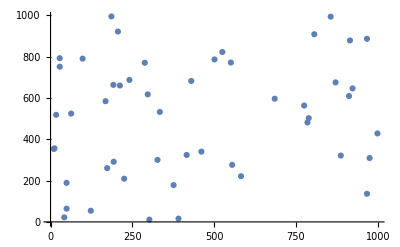

```mathematica
n =50;
randxy = RandomInteger[{0,1000},{n,2}];
ListPlot[randxy]
```

```mathematica
randxy
```

{{12,356},{582,221},{525,822},{685,596},{17,518},{555,276},{49,189},{206,921},{327,300},{775,563},{430,682},{856,993},{967,136},{923,646},{288,770},{28,751},{334,532},{887,321},{241,687},{168,584},{225,209},{501,786},{28,792},{212,660},{192,663},{789,502},{967,886},{785,481},{63,524},{871,675},{912,609},{186,994},{376,178},{297,617},{461,340},{42,22},{193,291},{302,11},{975,309},{551,771},{999,428},{173,260},{98,790},{915,878},{806,908},{416,324},{49,64},{123,54},{10,353},{391,16}}

```mathematica
(*results = ParallelTable[{
s=runSim[randxy,i,.99,100];
Print["Length: " <>ToString[s[[2]]] <> " CF: " <> ToString[i] <> " Number: " <> ToString[j]];
Join[{i},s]
},{i,100,500,100},{j,5}];
results = Flatten[results[[]],2];
ListPlot[results[[All,1;;3;;2]],PlotStyle->PointSize[Large]]*)
```

```mathematica
Dynamic[temp]
Dynamic[N[minDistance]]
Dynamic[N[totalDistance[oldxy]]]
Dynamic[Length[posSwaps]]
Dynamic[
Show[ListLinePlot[minPath,PlotStyle->Red],
ListLinePlot[oldxy,PlotStyle->Blue]]
]
r1 = runSim[randxy,500,.99,200]
```

{5790.76,{1.,49.,7.,47.,36.,48.,38.,50.,33.,21.,42.,37.,9.,46.,35.,6.,2.,13.,18.,39.,41.,28.,26.,4.,10.,31.,14.,30.,27.,44.,12.,45.,40.,3.,22.,11.,17.,34.,19.,15.,8.,32.,43.,23.,16.,25.,24.,20.,29.,5.,1.}}

{{12,356},{10,353},{49,189},{49,64},{42,22},{123,54},{302,11},{391,16},{376,178},{225,209},{173,260},{193,291},{327,300},{416,324},{461,340},{555,276},{582,221},{967,136},{887,321},{975,309},{999,428},{785,481},{789,502},{685,596},{775,563},{912,609},{923,646},{871,675},{967,886},{915,878},{856,993},{806,908},{551,771},{525,822},{501,786},{430,682},{334,532},{297,617},{241,687},{288,770},{206,921},{186,994},{98,790},{28,792},{28,751},{192,663},{212,660},{168,584},{63,524},{17,518},{12,356}}

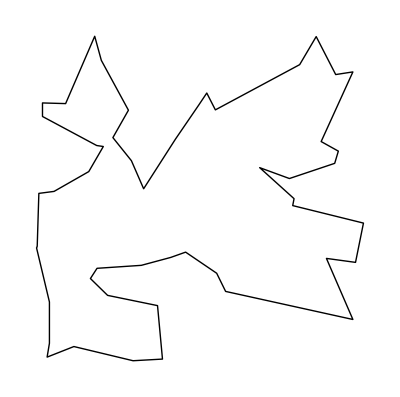

```mathematica
N[FindShortestTour[randxy]]
randxy[[Last[%]]]
Graphics[Line[%]]
```